## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PGCD";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_trp.csv";

mainFolder = "fit_PGCD_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName,  assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{3pg,Km or S05 substrate}

{0.0012,Km or S05 value}

{{{3pg,Null}},kcat substrates}

{0.55,kcat value}

{3pg,Other parameter susbtrate}

{183,Other parameter value}

{3php,Inhibition or activation constant substrate}

{5.4×10^-6,Inhibition or activation constant value}

{3pg,Inhibition or activation constant substrate}

{3.8×10^-6,Inhibition or activation constant value}

{3php,Km or S05 substrate}

{3.2×10^-6,Km or S05 value}

{{{3php,Null}},kcat substrates}

{27.8,kcat value}

{3php,Other parameter susbtrate}

{9270,Other parameter value}

{3pg,Km or S05 substrate}

{0.00049,Km or S05 value}

{{{3pg,Null}},kcat substrates}

{13.5,kcat value}

{3pg,Other parameter susbtrate}

{4610,Other parameter value}

{nadh,Km or S05 substrate}

{0.00012,Km or S05 value}

{3php,Km or S05 substrate}

{0.00035,Km or S05 value}

{3pg,Km or S05 substrate}

{0.00119,Km or S05 value}

{nad,Km or S05 substrate}

{0.00001,Km or S05 value}

{nad,Null;3pg,Null;,Keq substrate}

{3.9×10^-6,Keq value}

((3pg)^c+nad^c⇌(3php)^c+nadh^c)^PGCD

Null;

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad,Null;3pg,Null; | 3.9×10^-6 | 3.705×10^-6
4.095×10^-6 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.0012 | 0.00114
0.00126 | nad | 0.001 | M | 8.8 | 37 | trishcl | 0.04 | 
1 | 3php | 3.2×10^-6 | 3.04×10^-6
3.36×10^-6 | nadh | 0.00025 | M | 7.5 | 37 | kpi | 0.04 | 
1 | 3pg | 0.00049 | 0.00046
0.00052 | nadh | 0.00025 | M | 7.5 |  | kpi | 0.02 | 
1 | nadh | 0.00012 | 0.000114
0.000126 | 3php | 0.00009 | M | 7.1 | 30 | hepes | 0.025 | k | 0.0004
cl | 0.0004
1 | 3php | 0.00035 | 0.0003325
0.0003675 | nadh | 0.0001 | M | 7.1 | 30 | hepes | 0.025 | k | 0.0004
cl | 0.0004
1 | 3pg | 0.00119 | 0.0011305
0.0012495 | nad | 0.0005 | M | 9 | 30 | trishcl | 0.02 | 
1 | nad | 0.00001 | 9.5×10^-6
0.0000105 | 3pg | 0.005 | M | 9 | 30 | trishcl | 0.02 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 0.55 | 0.5225
0.5775 | 1/s | 8.8 | 37 | trishcl | 0.04 | 
1 | 3php | Null | 27.8 | 26.41
29.19 | 1/s | 7.5 | 37 | kpi | 0.04 | 
1 | 3pg | Null | 13.5 2.5^(0.1 (37-)) | 12.825 2.5^(0.1 (37-))
14.175 2.5^(0.1 (37-)) | 1/s | 7.5 | 37 | kpi | 0.02 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | ki | 3php | 5.4×10^-6 | 5.13×10^-6
5.67×10^-6 | nad | 0.001 |  |  | 8.8 | 37 | trishcl | 0.04 | 
1 | ki | 3pg | 3.8×10^-6 | 3.61×10^-6
3.99×10^-6 | nad | 0.001 |  | M | 8.8 | 37 | trishcl | 0.04 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | vmax | 3pg | 183 | 173.85
192.15 | nad | 0.001 | U/mg | 8.8 | 37 | trishcl | 0.04 | 
1 | vmax | 3php | 9270 | 8806.5
9733.5 | nadh | 0.00025 | U/mg | 7.5 | 37 | kpi | 0.04 | 
1 | vmax | 3pg | 4610 | 4550.
4670 | nadh | 0.00025 | U/mg | 7.5 |  | kpi | 0.02 |

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)


KeqPriorities = {1};
kmPriorities = {0,0,0,1,1,1,1};
s05Priorities = Null;
kcatPriorities = {1,0,0};
inhibitionPriorities={0,0};
activationPriorities = Null;
otherParamsPriorities = {0,0,0};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((3pg)^c+nad^c⇌(3php)^c+nadh^c)^PGCD

Null;

Structure: 4

Active sites: 1

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad,Null;3pg,Null; | 3.9×10^-6 | 3.705×10^-6
4.095×10^-6 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadh | 0.00012 | 0.000114
0.000126 | 3php | 0.00009 | M | 7.1 | 30 | hepes | 0.025 | k | 0.0004
cl | 0.0004
1 | 3php | 0.00035 | 0.0003325
0.0003675 | nadh | 0.0001 | M | 7.1 | 30 | hepes | 0.025 | k | 0.0004
cl | 0.0004
1 | 3pg | 0.00119 | 0.0011305
0.0012495 | nad | 0.0005 | M | 9 | 30 | trishcl | 0.02 | 
1 | nad | 0.00001 | 9.5×10^-6
0.0000105 | 3pg | 0.005 | M | 9 | 30 | trishcl | 0.02 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 0.55 | 0.5225
0.5775 | 1/s | 8.8 | 37 | trishcl | 0.04 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PGCD[c] + 3pg[c] <=> E_PGCD[c]&3pg",
				"E_PGCD[c]&3pg + nad[c] <=> E_PGCD[c]&3pg&nad",
				"E_PGCD[c]&3pg&nad <=> E_PGCD[c]&3php&nadh",
				"E_PGCD[c]&3php&nadh <=> E_PGCD[c]&3php + nadh[c]",
				"E_PGCD[c]&3php <=> E_PGCD[c] + 3php[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PGCD^c)_^+(3pg)^c⇌(PGCD^c&(3pg)^c)_^)^PGCD1,((PGCD^c&(3php)^c)_^⇌(PGCD^c)_^+(3php)^c)^PGCD2,((PGCD^c&(3pg)^c)_^+nad^c⇌(PGCD^c&(3pg)^c&nad^c)_^)^PGCD3,((PGCD^c&(3php)^c&nadh^c)_^⇌(PGCD^c&(3php)^c)_^+nadh^c)^PGCD4,((PGCD^c&(3pg)^c&nad^c)_^⇌(PGCD^c&(3php)^c&nadh^c)_^)^PGCD5}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGCD^c)_^+(3pg)^c⇌(PGCD^c&(3pg)^c)_^)^PGCD1,Overscript[(PGCD^c&(3php)^c)_^⇌(PGCD^c)_^+(3php)^c, PGCD2],((PGCD^c&(3pg)^c)_^+nad^c⇌(PGCD^c&(3pg)^c&nad^c)_^)^PGCD3,Overscript[(PGCD^c&(3php)^c&nadh^c)_^⇌(PGCD^c&(3php)^c)_^+nadh^c, PGCD4],((PGCD^c&(3pg)^c&nad^c)_^⇌(PGCD^c&(3php)^c&nadh^c)_^)^PGCD5};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{(3pg)^c→0,nad^c→0}

{(3php)^c→0,nadh^c→0}

{(3pg)^c→∞,nad^c→∞}

{(3php)^c→∞,nadh^c→∞}

Added inhibition reactions:

{}

Loading flux equation...

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Loading relative rate reverse equation...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	3pg[c]	3php[c]	nad[c]	nadh[c]	param_PGCD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/haldaneRatio_1.txt"	3.9e-6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/haldaneRatio_1.txt"	3.9e-6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/haldaneRatio_1.txt"	3.9e-6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/haldaneRatio_1.txt"	3.9e-6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/haldaneRatio_1.txt"	3.9e-6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/haldaneRatio_1.txt"	3.9e-6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/haldaneRatio_1.txt"	3.9e-6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/haldaneRatio_1.txt"	3.9e-6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/haldaneRatio_1.txt"	3.9e-6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/haldaneRatio_1.txt"	3.9e-6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/haldaneRatio_1.txt"	3.9e-6
1	0	0.00009	0	0.000012000000000000007	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_nadh.txt"	0.09090909090909095
1	0	0.00009	0	0.00001901871830953338	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_nadh.txt"	0.13680688860321014
1	0	0.00009	0	0.000030142637178115006	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_nadh.txt"	0.20076000891310197
1	0	0.00009	0	0.00004777286046641966	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_nadh.txt"	0.28474724895080133
1	0	0.00009	0	0.0000757148813376232	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_nadh.txt"	0.386863179846857
1	0	0.00009	0	0.00012000000000000008	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_nadh.txt"	0.5000000000000002
1	0	0.00009	0	0.00019018718309533382	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_nadh.txt"	0.6131368201531432
1	0	0.00009	0	0.00030142637178115007	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_nadh.txt"	0.7152527510491989
1	0	0.00009	0	0.0004777286046641971	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_nadh.txt"	0.7992399910868982
1	0	0.00009	0	0.0007571488133762321	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_nadh.txt"	0.86319311139679
1	0	0.00009	0	0.0012000000000000008	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_nadh.txt"	0.9090909090909091
1	0	0.000035000000000000004	0	0.0001	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_3php.txt"	0.09090909090909093
1	0	0.000055471261736139	0	0.0001	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_3php.txt"	0.13680688860321008
1	0	0.00008791602510283538	0	0.0001	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_3php.txt"	0.2007600089131019
1	0	0.0001393375096937241	0	0.0001	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_3php.txt"	0.28474724895080145
1	0	0.00022083507056806757	0	0.0001	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_3php.txt"	0.3868631798468569
1	0	0.00035000000000000005	0	0.0001	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_3php.txt"	0.5
1	0	0.0005547126173613899	0	0.0001	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_3php.txt"	0.6131368201531431
1	0	0.0008791602510283538	0	0.0001	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_3php.txt"	0.7152527510491987
1	0	0.0013933750969372409	0	0.0001	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_3php.txt"	0.7992399910868982
1	0	0.0022083507056806758	0	0.0001	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_3php.txt"	0.8631931113967899
1	0	0.0035	0	0.0001	1	7.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_3php.txt"	0.9090909090909091
1	0.00011899999999999995	0	0.0005	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_3pg.txt"	0.09090909090909087
1	0.0001886022899028725	0	0.0005	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_3pg.txt"	0.13680688860321
1	0.0002989144853496399	0	0.0005	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_3pg.txt"	0.20076000891310167
1	0.00047374753295866164	0	0.0005	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_3pg.txt"	0.28474724895080133
1	0.0007508392399314301	0	0.0005	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_3pg.txt"	0.386863179846857
1	0.0011899999999999994	0	0.0005	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_3pg.txt"	0.4999999999999999
1	0.0018860228990287252	0	0.0005	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_3pg.txt"	0.6131368201531431
1	0.0029891448534963986	0	0.0005	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_3pg.txt"	0.7152527510491984
1	0.004737475329586616	0	0.0005	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_3pg.txt"	0.7992399910868982
1	0.007508392399314301	0	0.0005	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_3pg.txt"	0.86319311139679
1	0.011899999999999996	0	0.0005	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_3pg.txt"	0.9090909090909091
1	0.005	0	1.e-6	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_nad.txt"	0.0909090909090909
1	0.005	0	1.584893192461114e-6	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_nad.txt"	0.13680688860321005
1	0.005	0	2.5118864315095823e-6	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_nad.txt"	0.2007600089131019
1	0.005	0	3.981071705534969e-6	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_nad.txt"	0.2847472489508012
1	0.005	0	6.30957344480193e-6	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_nad.txt"	0.38686317984685686
1	0.005	0	0.00001	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_nad.txt"	0.49999999999999994
1	0.005	0	0.00001584893192461114	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_nad.txt"	0.613136820153143
1	0.005	0	0.000025118864315095822	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_nad.txt"	0.7152527510491987
1	0.005	0	0.000039810717055349695	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_nad.txt"	0.7992399910868981
1	0.005	0	0.00006309573444801929	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_nad.txt"	0.8631931113967899
1	0.005	0	0.0001	0	1	9	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0.01	0	0.01	0	1	8.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/absRateFor.txt"	0.55
1	0.01	0	0.01	0	1	8.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/absRateFor.txt"	0.55
1	0.01	0	0.01	0	1	8.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/absRateFor.txt"	0.55
1	0.01	0	0.01	0	1	8.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/absRateFor.txt"	0.55
1	0.01	0	0.01	0	1	8.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/absRateFor.txt"	0.55
1	0.01	0	0.01	0	1	8.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/absRateFor.txt"	0.55
1	0.01	0	0.01	0	1	8.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/absRateFor.txt"	0.55
1	0.01	0	0.01	0	1	8.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/absRateFor.txt"	0.55
1	0.01	0	0.01	0	1	8.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/absRateFor.txt"	0.55
1	0.01	0	0.01	0	1	8.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/absRateFor.txt"	0.55
1	0.01	0	0.01	0	1	8.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/absRateFor.txt"	0.55

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_3pg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_nad.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_3php.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_nadh.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_3pg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateFor_nad.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_3php.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/relRateRev_nadh.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGCD_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 2.95652397956
best_fit: 2.95688776219
best_fit: 2.38181421321
best_fit: 2.95706063188
best_fit: 2.95630383825

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.000578335 | 3.34472×10^-7 | 5.19696×10^-9 | 0.133255 | 3.9×10^-6 | 3.9052×10^-6
1 | haldaneRatio_1 | 0.000578335 | 3.34472×10^-7 | 5.19696×10^-9 | 0.133255 | 3.9×10^-6 | 3.9052×10^-6
1 | haldaneRatio_1 | 0.000578335 | 3.34472×10^-7 | 5.19696×10^-9 | 0.133255 | 3.9×10^-6 | 3.9052×10^-6
1 | haldaneRatio_1 | 0.000578335 | 3.34472×10^-7 | 5.19696×10^-9 | 0.133255 | 3.9×10^-6 | 3.9052×10^-6
1 | haldaneRatio_1 | 0.000578335 | 3.34472×10^-7 | 5.19696×10^-9 | 0.133255 | 3.9×10^-6 | 3.9052×10^-6
1 | haldaneRatio_1 | 0.000578335 | 3.34472×10^-7 | 5.19696×10^-9 | 0.133255 | 3.9×10^-6 | 3.9052×10^-6
1 | haldaneRatio_1 | 0.000578335 | 3.34472×10^-7 | 5.19696×10^-9 | 0.133255 | 3.9×10^-6 | 3.9052×10^-6
1 | haldaneRatio_1 | 0.000578335 | 3.34472×10^-7 | 5.19696×10^-9 | 0.133255 | 3.9×10^-6 | 3.9052×10^-6
1 | haldaneRatio_1 | 0.000578335 | 3.34472×10^-7 | 5.19696×10^-9 | 0.133255 | 3.9×10^-6 | 3.9052×10^-6
1 | haldaneRatio_1 | 0.000578335 | 3.34472×10^-7 | 5.19696×10^-9 | 0.133255 | 3.9×10^-6 | 3.9052×10^-6
1 | haldaneRatio_1 | 0.000578335 | 3.34472×10^-7 | 5.19696×10^-9 | 0.133255 | 3.9×10^-6 | 3.9052×10^-6
1 | relRateRev_nadh | 0.29009 | 0.084152 | 0.0863861 | 95.0247 | 0.0909091 | 0.177295
1 | relRateRev_nadh | 0.269739 | 0.0727589 | 0.117786 | 86.0966 | 0.136807 | 0.254593
1 | relRateRev_nadh | 0.242883 | 0.0589923 | 0.150445 | 74.9377 | 0.20076 | 0.351205
1 | relRateRev_nadh | 0.209964 | 0.0440847 | 0.17702 | 62.1674 | 0.284747 | 0.461767
1 | relRateRev_nadh | 0.173033 | 0.0299405 | 0.18936 | 48.9475 | 0.386863 | 0.576223
1 | relRateRev_nadh | 0.13548 | 0.0183548 | 0.183046 | 36.6091 | 0.5 | 0.683046
1 | relRateRev_nadh | 0.100917 | 0.0101842 | 0.160388 | 26.1586 | 0.613137 | 0.773525
1 | relRateRev_nadh | 0.0719196 | 0.00517243 | 0.128819 | 18.0102 | 0.715253 | 0.844071
1 | relRateRev_nadh | 0.049441 | 0.00244441 | 0.0963685 | 12.0575 | 0.79924 | 0.895608
1 | relRateRev_nadh | 0.0330722 | 0.00109377 | 0.0683011 | 7.91261 | 0.863193 | 0.931494
1 | relRateRev_nadh | 0.0216937 | 0.000470615 | 0.0465638 | 5.12201 | 0.909091 | 0.955655
1 | relRateRev_3php | 0.289889 | 0.0840355 | 0.0863041 | 94.9345 | 0.0909091 | 0.177213
1 | relRateRev_3php | 0.269556 | 0.0726607 | 0.117679 | 86.0186 | 0.136807 | 0.254486
1 | relRateRev_3php | 0.242725 | 0.0589154 | 0.150317 | 74.8739 | 0.20076 | 0.351077
1 | relRateRev_3php | 0.209832 | 0.0440295 | 0.17688 | 62.1183 | 0.284747 | 0.461628
1 | relRateRev_3php | 0.17293 | 0.0299046 | 0.189222 | 48.912 | 0.386863 | 0.576086
1 | relRateRev_3php | 0.135402 | 0.0183338 | 0.182924 | 36.5848 | 0.5 | 0.682924
1 | relRateRev_3php | 0.100861 | 0.010173 | 0.160289 | 26.1425 | 0.613137 | 0.773426
1 | relRateRev_3php | 0.0718815 | 0.00516695 | 0.128745 | 17.9999 | 0.715253 | 0.843997
1 | relRateRev_3php | 0.0494155 | 0.00244189 | 0.0963159 | 12.0509 | 0.79924 | 0.895556
1 | relRateRev_3php | 0.0330555 | 0.00109266 | 0.0682652 | 7.90845 | 0.863193 | 0.931458
1 | relRateRev_3php | 0.0216828 | 0.000470145 | 0.0465399 | 5.11939 | 0.909091 | 0.955631
1 | relRateFor_3pg | 0.0007056 | 4.97872×10^-7 | 0.000147821 | 0.162603 | 0.0909091 | 0.0910569
1 | relRateFor_3pg | 0.000669949 | 4.48831×10^-7 | 0.000211203 | 0.15438 | 0.136807 | 0.137018
1 | relRateFor_3pg | 0.000620278 | 3.84744×10^-7 | 0.000286939 | 0.142926 | 0.20076 | 0.201047
1 | relRateFor_3pg | 0.000555055 | 3.08086×10^-7 | 0.000364157 | 0.127888 | 0.284747 | 0.285111
1 | relRateFor_3pg | 0.000475767 | 2.26354×10^-7 | 0.000424038 | 0.109609 | 0.386863 | 0.387287
1 | relRateFor_3pg | 0.000387938 | 1.50496×10^-7 | 0.00044683 | 0.089366 | 0.5 | 0.500447
1 | relRateFor_3pg | 0.000300128 | 9.00767×10^-8 | 0.000423867 | 0.0691309 | 0.613137 | 0.613561
1 | relRateFor_3pg | 0.000220886 | 4.87907×10^-8 | 0.000363877 | 0.0508739 | 0.715253 | 0.715617
1 | relRateFor_3pg | 0.000155723 | 2.42498×10^-8 | 0.000286632 | 0.0358631 | 0.79924 | 0.799527
1 | relRateFor_3pg | 0.000106111 | 1.12595×10^-8 | 0.000210929 | 0.0244359 | 0.863193 | 0.863404
1 | relRateFor_3pg | 0.0000705085 | 4.97144×10^-9 | 0.000147604 | 0.0162365 | 0.909091 | 0.909239
1 | relRateFor_nad | 0.00267337 | 7.14692×10^-6 | 0.000557887 | 0.613676 | 0.0909091 | 0.0903512
1 | relRateFor_nad | 0.00253879 | 6.44547×10^-6 | 0.000797411 | 0.582873 | 0.136807 | 0.136009
1 | relRateFor_nad | 0.0023512 | 5.52816×10^-6 | 0.00108395 | 0.539922 | 0.20076 | 0.199676
1 | relRateFor_nad | 0.00210473 | 4.42988×10^-6 | 0.00137664 | 0.483459 | 0.284747 | 0.283371
1 | relRateFor_nad | 0.00180486 | 3.25753×10^-6 | 0.00160441 | 0.414722 | 0.386863 | 0.385259
1 | relRateFor_nad | 0.00147239 | 2.16793×10^-6 | 0.00169228 | 0.338456 | 0.5 | 0.498308
1 | relRateFor_nad | 0.00113966 | 1.29883×10^-6 | 0.00160687 | 0.262073 | 0.613137 | 0.61153
1 | relRateFor_nad | 0.00083913 | 7.04139×10^-7 | 0.00138065 | 0.19303 | 0.715253 | 0.713872
1 | relRateFor_nad | 0.000591794 | 3.5022×10^-7 | 0.00108835 | 0.136173 | 0.79924 | 0.798152
1 | relRateFor_nad | 0.000403363 | 1.62701×10^-7 | 0.000801341 | 0.0928346 | 0.863193 | 0.862392
1 | relRateFor_nad | 0.000268079 | 7.18663×10^-8 | 0.000560985 | 0.0617084 | 0.909091 | 0.90853
1 | absRateFor | 0.000312208 | 9.74738×10^-8 | 0.000395245 | 0.0718627 | 0.55 | 0.549605
1 | absRateFor | 0.000312208 | 9.74738×10^-8 | 0.000395245 | 0.0718627 | 0.55 | 0.549605
1 | absRateFor | 0.000312208 | 9.74738×10^-8 | 0.000395245 | 0.0718627 | 0.55 | 0.549605
1 | absRateFor | 0.000312208 | 9.74738×10^-8 | 0.000395245 | 0.0718627 | 0.55 | 0.549605
1 | absRateFor | 0.000312208 | 9.74738×10^-8 | 0.000395245 | 0.0718627 | 0.55 | 0.549605
1 | absRateFor | 0.000312208 | 9.74738×10^-8 | 0.000395245 | 0.0718627 | 0.55 | 0.549605
1 | absRateFor | 0.000312208 | 9.74738×10^-8 | 0.000395245 | 0.0718627 | 0.55 | 0.549605
1 | absRateFor | 0.000312208 | 9.74738×10^-8 | 0.000395245 | 0.0718627 | 0.55 | 0.549605
1 | absRateFor | 0.000312208 | 9.74738×10^-8 | 0.000395245 | 0.0718627 | 0.55 | 0.549605
1 | absRateFor | 0.000312208 | 9.74738×10^-8 | 0.000395245 | 0.0718627 | 0.55 | 0.549605
1 | absRateFor | 0.000312208 | 9.74738×10^-8 | 0.000395245 | 0.0718627 | 0.55 | 0.549605

### Simulated Data and Best Fit Data Plot

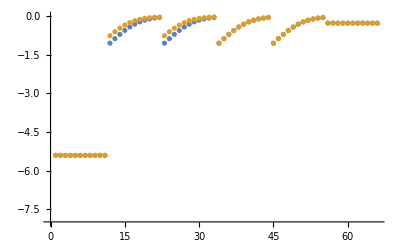

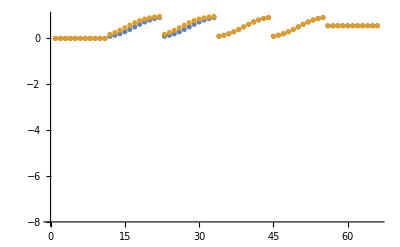

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

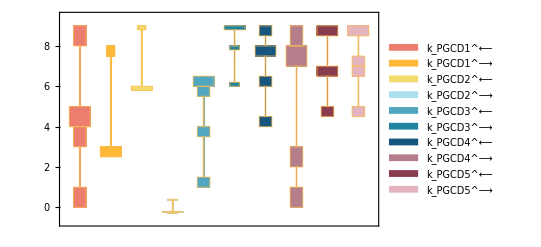

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

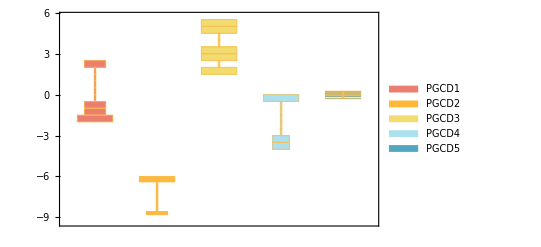

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

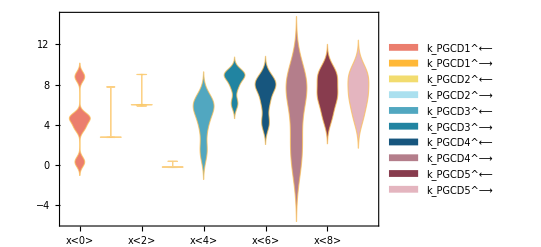

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

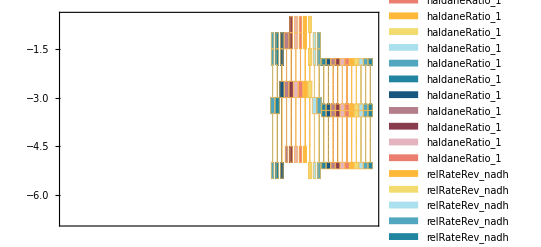

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.00012 | 0.0000556837 | 53.5969
0.00035 | 0.000162502 | 53.5708
0.00119 | 0.00118787 | 0.178572
0.00001 | 0.0000100679 | 0.679212

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
0.55 | (1.76817×10^24 nad^c)/(2.90571×10^24 nad^c+0.608514 (2.91628×10^19+5.08903×10^23 nad^c)) | 181.818 Abs[0.55-(1.76817×10^24 nad^c)/(2.90571×10^24 nad^c+0.608514 (2.91628×10^19+5.08903×10^23 nad^c))]

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

data value | predicted value | error in %
{}⟦1⟧⟦3⟧ | 1 | (100 Abs[-1+{}⟦1⟧⟦3⟧])/({}⟦1⟧⟦3⟧)

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
3.9×10^-6 | 3.9052×10^-6 | 0.133255